# Functions

```mathematica
(*setup the data import*)

setup[string_]:=(
fitfn=StringJoin[string,".fit"];
fit=Import[fitfn,"CSV"];
datafn=StringJoin[string,".dat"];
data=Transpose[Transpose[Import[datafn,"CSV"]][[1;;2]]];
mzfit=Transpose[fit][[1]];
mzdata=Transpose[data][[1]];
Clear[rangeaccesshash];
);

setuprange:=((*find the fitless range*)

values=Transpose[fit][[2]];
valuesLength=Length[values];
punit=IntegerPart[valuesLength/8];
partition=Partition[values,punit][[1;;7]];
ran=range/@partition;
Do[rangeaccesshash[ran[[i]]]=i,{i,1,Length[ran]}];

(*start expanding "fitless" region from center point and endpoint*)
minrange=Min[ran];
min=rangeaccesshash[minrange];
baseline=Mean[partition[[min]]];
{leftborder,rightborder}={(min-1)*punit+1,min*punit};
{peak1rightborder,peak2leftborder}=creepUp[leftborder,rightborder,1000,values,#]&/@{-1,1};
peak2rightborder=creepUp[valuesLength,valuesLength,1000,values,-1];
peak1leftborder=creepUp[1,1,1000,values,+1];
fitlessrange={peak1leftborder,peak1rightborder,peak2leftborder,peak2rightborder};

(*protect against using single isotope peaks in datascale*)
{FLR1,FLR2}={{#1,#2},{#3,#4}}&[Sequence@@fitlessrange];
If[Sign[First[Differences[FLR1]]]<0||Sign[First[Differences[FLR2]]]<0,Next[],
datascale=Min[Max[Transpose[fit[[#[[1]];;#[[2]]  ]]][[2]]  ]&/@{FLR1,FLR2}];
];
);

(*function definition*)
range[x_List]:=Max[x]-Min[x];

(*algorithm to find the left and right endpoints of "fitless" region*)
creepUp[LB_,RB_,EA_,Val_List,direction_]:=
({TLB,TRB,TEA}={LB,RB,EA};
If[direction<0,
While[TEA>50&&TLB-TEA≥0,
temprange=Val[[TLB-TEA;;RB]];
If[range[temprange]<10 minrange,TLB=TLB-TEA;(*Print[range[temprange],":",TLB];*)   ];
If[range[temprange]>10minrange,TEA=IntegerPart[TEA/2];(*Print[TEA];*) ];
];
Return[TLB]
];

If[direction>0,
While[TEA>50&&TRB+TEA≤Length[fit],
temprange=Val[[LB;;TRB+TEA]];
If[range[temprange]<10minrange,TRB=TRB+TEA];
If[range[temprange]>10minrange,TEA=IntegerPart[TEA/2]];
];
Return[TRB];
Print[TRB];
];

)

xcoord[x_Integer]:=fit[[x]][[1]];

mzplot[fitlessrange_List]:=(
lines=Line[{{xcoord[#],0},{xcoord[#],1/10 Max[values]}}]&/@fitlessrange;
grafx=Graphics[{Thick,Red,Dashed,#}]&/@lines;
plot=ListPlot[{fit,data},PlotRange->{All,{0,2000}},Joined->True,PlotStyle->{{Thick,Blue},{Green,Thick,Dashed}}];
Show[plot,grafx,PlotRange->All,Frame->True,LabelStyle->Directive[32,FontFamily->"Arial"],FrameLabel->{"m/z","Intensity"}]);

(*distance functions*)
powersdifference[point_List,n_]:=Total[(#[[1]]-#[[2]])^n&/@point];
absdifference[point_List]:=Total[Abs[(#[[1]]-#[[2]])]&/@point];

(*finds the peaks within the region fed to it (FLR1,FLR2)*)
findpeaks[FLR_List]:=(
abovebelow=-1;
peaks={};
temppeaks={};
Do[
If[Sign[fit[[i]][[2]]-1.1*baseline]≠abovebelow,
AppendTo[temppeaks,i ];
abovebelow*=-1;];

If[Length[temppeaks]==2,
peakscale=Max[fit[[#[[1]];;#[[2]]]]]&[temppeaks];
If[peakscale>datascale/25,
AppendTo[peaks,temppeaks];
];
temppeaks={}
];

,{i,#1,#2}]&[Sequence@@FLR];
Return[peaks]
);

(*makes pairs between data and fit points within the region fed to it*)
pairmaker[peaks_List]:=((*pairmaker*)
peakendpoints=peaks;
nearestdata=Nearest[mzdata];nearestfit=Nearest[mzfit];
expandedpeakendpoints=First[nearestfit[nearestdata[mzfit[[peakendpoints[[#]]]]][[1]]]]&/@{1,2};
expandedpeakendpoints=Sequence@@Flatten[Position[mzfit,#]]&/@expandedpeakendpoints;
tempregionfit=fit[[#1;;#2]]&[Sequence@@expandedpeakendpoints];

nearesttempfit=Nearest[Transpose[tempregionfit][[1]]];

dataendpointsmz=Flatten[nearestdata[#]&/@(tempregionfit[[#]][[1]]&/@{1,-1})];
dataendpointsindex=Sequence@@First[Position[mzdata,#]]&/@dataendpointsmz;
tempregiondata=Transpose[Transpose[data[[#1;;#2]]&[Sequence@@dataendpointsindex]][[1;;2]]];
datapairs={};

Do[
{dataposition,datavalue}=tempregiondata[[i]];
fitposition=First[Flatten[Position[tempregionfit,First[nearesttempfit[dataposition]]]]];
fitvalue=tempregionfit[[fitposition]][[2]];
AppendTo[datapairs,{datavalue,fitvalue}];

,{i,1,Length[tempregiondata]}];
Return[datapairs];
);

(*calculates the relative error of a given peak*)

score[peakchoice_]:=
(

datapairs=pairmaker[peakchoice];
absdiff=absdifference[datapairs];
absarea=Total[Transpose[datapairs][[2]]];
absdiff/absarea
(*maxdiff=Abs[(#[[1]]-#[[2]])/#[[2]]&[Max[##]&/@(Transpose[pairmaker[peakchoice]][[#]]&/@{1,2})]];
Return[maxdiff];*)


);

(*actually scores the data*)

doscoring:=(peaks=(findpeaks[#]&/@{FLR1,FLR2});
scorecollection=(score[#]&/@peaks[[#]]&/@{1,2});
tempscore=Max[scorecollection[[#]]](*/Min[scorecollection[[#]]]*)&/@{1,2};
tempscore=Max[tempscore];
);

(*makes a mouseover plot of peptide, score and fit plot*)

tooltipplot:=(tooltipscores={};
Do[temppic=Import[StringJoin[sortedscores[[i]][[1]],".fit.png"]];
AppendTo[tooltipscores,Tooltip[ sortedscores[[i]][[2] ],temppic]];
,{i,1,Length[sortedscores]}];
ListPlot[tooltipscores,PlotStyle->Directive[PointSize[0.01]],Frame->True,LabelStyle->Directive[26,FontFamily->"Helvetica"],FrameLabel->{"peptide identity","penalty"},PlotRange->All,GridLines->Automatic]);
```

# Body

```mathematica
time1 = AbsoluteTime[];
SetDirectory["/Users/joshsilverman/Documents/Research/AutoFilter/sampledata"];
fn=Drop[FileNames[],1];
rawstrings=DeleteDuplicates[StringReplace[#,".png"|".contour"|".newcon"|".txt"|".dat"|".fit"->""]&/@fn];
```

```mathematica
scoretable={};
i=15;
(*Do[*)
setup[rawstrings[[i]]];
setuprange;
(*If[Min[Length[##]&/@scorecollection]>1,*)
If[Sign[First[Differences[FLR1]]]<0||Sign[First[Differences[FLR2]]]<0,Next[];Print["flopped"],
doscoring

If[datascale<10*baseline,Next[],
AppendTo[scoretable,{rawstrings[[i]],tempscore}];
];


];
(*];*)
Print[rawstrings[[i]]];
Print[AbsoluteTime[]-time1];
(*,{i,1,7(*Length[rawstrings]*)}];*)
sortedscores=SortBy[scoretable,Last];
```

L11_52_65_0_756.943407334785_81.365

2.46997

```mathematica
3
```

3

# stuff

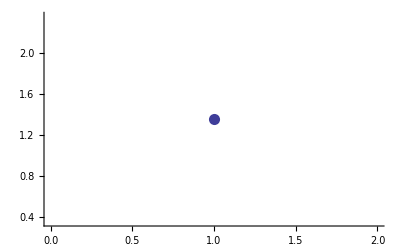

```mathematica
TableForm[sortedscores];
ListPlot[Transpose[sortedscores][[2]],PlotStyle->Directive[PointSize[0.02]],PlotRange->All]
```

Import::nffil: File not found during Import.

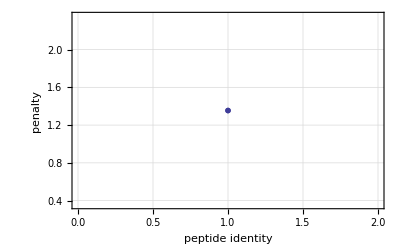

```mathematica
tooltipplot
```

```mathematica
creepUp[1,1,1000,values,+1]
```

1251

# Export

```mathematica
SetDirectory["/Users/bubbloy/Desktop"];
Export["GelTwoAndThree_scores_Sunday.txt",scoretable,"Table"];
```

SetDirectory::cdir: Cannot set current directory to /Users/bubbloy/Desktop.

```mathematica
Length[scoretable]
```

1

# Images

```mathematica
(*rawstring=sortedscores[[2]][[1]];
setup[rawstring]//Quiet;
setuprange;
peaks=(Flatten[findpeaks[#]&/@{FLR1,FLR2},1]);
flatpeaks=Flatten[peaks];
a=mzplot[flatpeaks]
sortedscores[[2]]*)
```

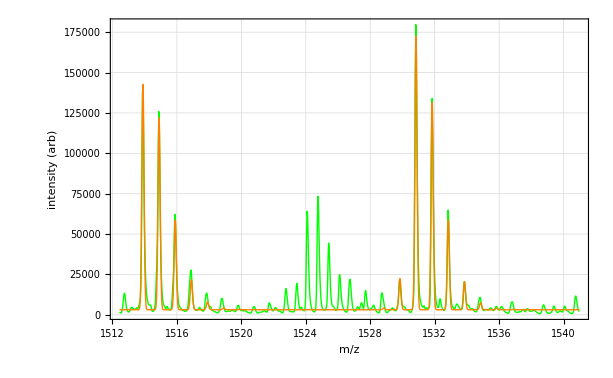

```mathematica
ListPlot[{data,fit},PlotRange->All,PlotStyle->{{Thick,Green},{Thick,Orange}},Joined->True,Frame->True,FrameLabel->{"m/z","intensity (arb)"},LabelStyle->Directive[FontFamily->"Helvetica", 32],GridLines->Automatic]
```